Computing the eigenvalues of H using numerical approach

### The q-ratio is properly chosen and avoids strong oscillating behavior of λ near certain points across q-interval

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e,n-m==0},{Sqrt[m+1]Sqrt[m+2](-v),n-m==2},{Sqrt[m]Sqrt[m-1](-v),n-m==-2 }}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_,q_]:=Hmat02[n,1,q];
boson1[n_,q_]:=Hmat13[n,1,q];
```

Solutions of the matrix Hamiltonian

```mathematica
sol0[n_,q_]:=Eigenvalues[boson0[n,q]];
sol1[n_,q_]:=Eigenvalues[boson1[n,q]];
```

Evolution of λ with the ratio q

```mathematica
lambdaQ[n_,id_,p_]:=sol0[n,q][[id]]/.{q->p};
```

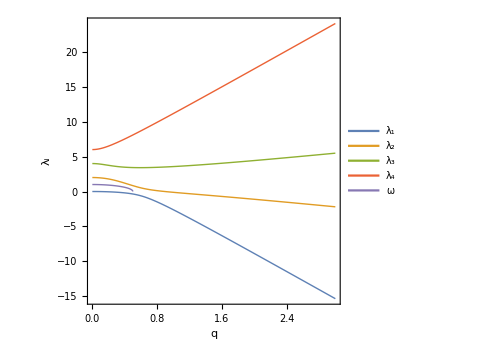

```mathematica
Plot[{lambdaQ[4,1,p],lambdaQ[4,2,p],lambdaQ[4,3,p],lambdaQ[4,4,p],Sqrt[1-4p^2]},{p,0,3},AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],LabelStyle->{Black,20,Bold,FontFamily->"Times New Roman"},FrameLabel->{"q",Subscript["λ","i"]},PlotLegends->Placed[{"λ_1","λ_2","λ_3","λ_4","ω"},{0.15,0.7}],ImageSize->Medium,PlotStyle->Thick]
```

## Table with λ’s for a given N

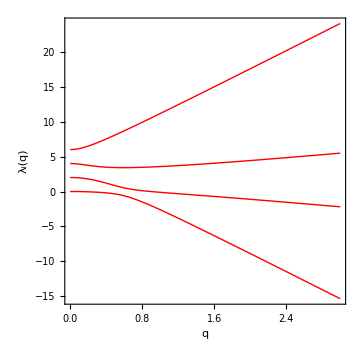

```mathematica
lambdaTable[n_,p_]:=Table[sol0[n,q][[pos]]/.{q->p},{pos,1,Length[sol0[n,q]]}];
tablePlot[n_]:=Plot[lambdaTable[n,p],{p,0,3},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->1,FrameLabel->{"q","λ_i(q)"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{{Red,Thick},{Blue,Thick}},ImageSize->Medium];
tablePlot[4]
```

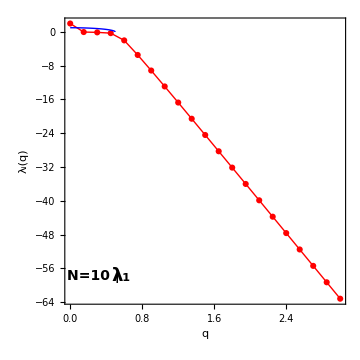
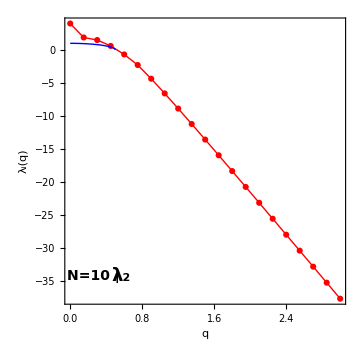
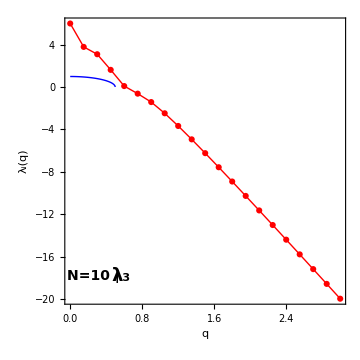
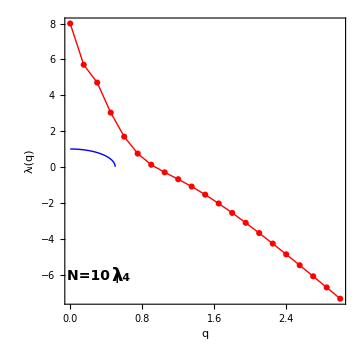
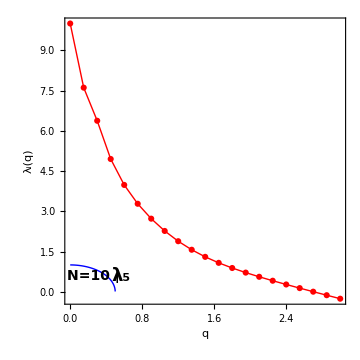
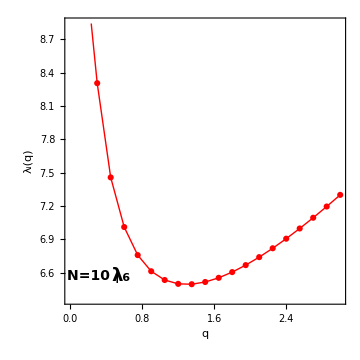
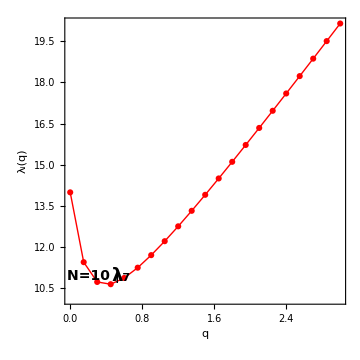
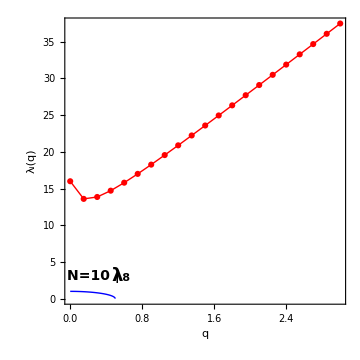

```mathematica
jointQs[n_,id_]:=Table[{i,lambdaQ[n,id,i]},{i,0,3,0.15}];
plots[n_]:=Table[Show[{ListLinePlot[jointQs[n,id],Frame->True,Axes->False,PlotMarkers->Automatic,FrameStyle->Directive[Black,Thick],Joined->True,AspectRatio->1,FrameLabel->{"q","λ_i(q)"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{Red,Thick},ImageSize->Medium,Epilog->{Inset[Style[StringTemplate["N=`` | "][n],14,Bold,Italic,FontFamily->"Times New Roman"],Scaled[{0.1,0.1}]],Inset[Style[StringTemplate["λ_(``)"][id],18,Bold,Italic,FontFamily->"Times New Roman"],Scaled[{0.2,0.1}]]}],Plot[Sqrt[1-4q^2],{q,0,3},PlotStyle->{Blue,Thick}]}],{id,1,n}];
plots[4]
```

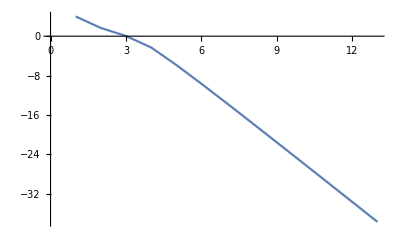

```mathematica
ListPlot[Table[N[lambdaQ[10,2,id]],{id,0.0,3.0,0.25}],Joined->True]
```

```mathematica
Do[Print[p,"\n",lambdaTable[10,p]],{p,0,3,1.5}]
```

0.
{2.,4.,6.,8.,10.,12.,14.,16.,18.,0.+0. ⅈ}

1.5
{-24.411,-13.5766,-6.2348,-1.54686,1.30077,6.51569,13.9104,23.5952,36.3132,54.134}

3.
{-63.1969,-37.6728,-19.9666,-7.34955,-0.259196,7.29987,20.1465,37.489,60.5231,92.9866}